```mathematica
Clear[KSx0,KSx1,KSx2,KSx3]
```

{KSx0→x0,KSx1→ⅇ^x1+R0,KSx2→x2,KSx3→x3}

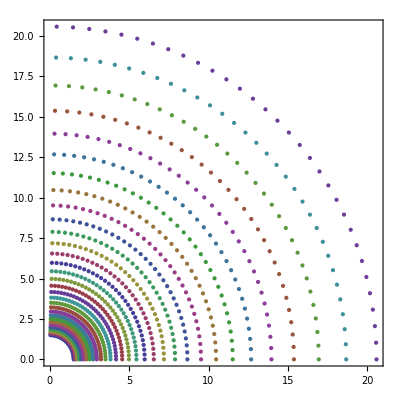

```mathematica
(* coordinate conversion *)
cx0=KSx0==x0;
cx3=KSx3==x3;
cx1=KSx1==R0+Exp[x1];
cx2=KSx2==x2;
suborg={cx0[[1]]->cx0[[2]],cx1[[1]]->cx1[[2]],cx2[[1]]->cx2[[2]],cx3[[1]]->cx3[[2]]}
grid=Table[{cx2[[2]],cx1[[2]]}/.{R0->.5},{x1,0,3,.1},{x2,0,π/2,.05}];
ListPolarPlot[grid,Frame->True]
```

```mathematica
(* inverse transformation *)
subinv={
icx0=Solve[cx0,x0][[1,1]],
icx1=x1->Log[KSx1-R0](* Solve[cx1,x1] *),
icx2=Solve[cx2,x2][[1,1]],
icx3=Solve[cx3,x3][[1,1]]}
```

{x0→KSx0,x1→Log[KSx1-R0],x2→KSx2,x3→KSx3}

```mathematica
XKSMKS={{D[cx0[[2]],x0],D[cx0[[2]],x1],D[cx0[[2]],x2],D[cx0[[2]],x3]},
{D[cx1[[2]],x0],D[cx1[[2]],x1],D[cx1[[2]],x2],D[cx1[[2]],x3]},
{D[cx2[[2]],x0],D[cx2[[2]],x1],D[cx2[[2]],x2],D[cx2[[2]],x3]},
{D[cx3[[2]],x0],D[cx3[[2]],x1],D[cx3[[2]],x2],D[cx3[[2]],x3]}}/.subinv;
TableForm[XKSMKS]
```

1 | 0 | 0 | 0
0 | KSx1-R0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
(* no coupling between various coordinates so this is simple *)
XMKSKS=Inverse[XKSMKS];
TableForm[XMKSKS]
```

1 | 0 | 0 | 0
0 | 1/(KSx1-R0) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

```mathematica
(* done with dXdX arrays so far *)
```

```mathematica
(* KS g_munu (-+++) *)
scoor = {r->KSx1,θ->KSx2, ϕ->KSx3};
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2r+a^2;
A=(r^2+a^2)^2-a^2 Δ Sin[θ]^2
g00=-(1-(2r)/Σ);
g03=g30=-(2r)/Σ a Sin[θ]^2;
g11=1+2 r/Σ;
g22=Σ;
g33=Sin[θ]^2(Σ+a^2(1+(2r)/Σ)Sin[θ]^2);
g01=g10=(2r)/Σ;
g13=g31=-a(1+(2r)/Σ)Sin[θ]^2;
g02=g12=g20=g21=g23=g32=0;
```

(a^2+r^2)^2-a^2 (a^2-2 r+r^2) Sin[θ]^2

```mathematica
(* matrix form *)
gKS=Simplify[{{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}}];
gKS=gKS/.scoor;
MatrixForm[gKS]
```

(-1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | (2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | -(2 a KSx1 Sin[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2)
(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | -a (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2
0 | 0 | KSx1^2+a^2 Cos[KSx2]^2 | 0
-(2 a KSx1 Sin[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2) | -a (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2 | 0 | Sin[KSx2]^2 (KSx1^2+a^2 Cos[KSx2]^2+a^2 (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2))

```mathematica
(* a=0 & testing *)
MatrixForm[gKS/.{a->0}]
```

(-1+2/KSx1 | 2/KSx1 | 0 | 0
2/KSx1 | 1+2/KSx1 | 0 | 0
0 | 0 | KSx1^2 | 0
0 | 0 | 0 | KSx1^2 Sin[KSx2]^2)

```mathematica
(* inversed metric g^munu *)
MatrixForm[GKS=Simplify[Inverse[gKS]]]
```

(-(KSx1 (2+KSx1)+a^2 Cos[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2) | (2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | 0
(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | (a^2+(-2+KSx1) KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | a/(KSx1^2+a^2 Cos[KSx2]^2)
0 | 0 | 1/(KSx1^2+a^2 Cos[KSx2]^2) | 0
0 | a/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | Csc[KSx2]^2/(KSx1^2+a^2 Cos[KSx2]^2))

```mathematica
GMKS=GKS;
For[i=1,i<=4,i++,
For[j=1,j<=4,j++,
GMKS[[i,j]]=0;
For[k=1,k<=4,k++,
For[l=1,l<=4,l++,
GMKS[[i,j]]=GMKS[[i,j]]+ XMKSKS[[i,k]] XMKSKS[[j,l]] GKS[[k,l]];
]
]
]
]
(* substituting MKS coordinates *)
GMKS=GMKS/.suborg;
TableForm[Simplify[GMKS]]
```

-((ⅇ^x1+R0) (2+ⅇ^x1+R0)+a^2 Cos[x2]^2)/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | (2 ⅇ^-x1 (ⅇ^x1+R0))/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | 0 | 0
(2 ⅇ^-x1 (ⅇ^x1+R0))/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | (ⅇ^(-2 x1) (a^2+(-2+ⅇ^x1+R0) (ⅇ^x1+R0)))/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | 0 | (a ⅇ^-x1)/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2)
0 | 0 | 1/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | 0
0 | (a ⅇ^-x1)/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) | 0 | Csc[x2]^2/((ⅇ^x1+R0)^2+a^2 Cos[x2]^2)

```mathematica
TableForm[gMKS=Simplify[Inverse[GMKS]]]
```

-(a^2+2 (ⅇ^(2 x1)+2 ⅇ^x1 (-1+R0)+(-2+R0) R0)+a^2 Cos[2 x2])/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]) | (4 ⅇ^x1 (ⅇ^x1+R0))/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]) | 0 | -(4 a (ⅇ^x1+R0) Sin[x2]^2)/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])
(4 ⅇ^x1 (ⅇ^x1+R0))/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]) | (4 ⅇ^(2 x1) (ⅇ^(2 x1)+2 ⅇ^x1 (1+R0)+R0 (2+R0)+a^2 Cos[x2]^2) ((ⅇ^x1+R0)^2+a^2 Cos[x2]^2))/((a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])^2) | 0 | -(4 a ⅇ^x1 (ⅇ^(2 x1)+2 ⅇ^x1 (1+R0)+R0 (2+R0)+a^2 Cos[x2]^2) ((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) Sin[x2]^2)/((a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])^2)
0 | 0 | (ⅇ^x1+R0)^2+a^2 Cos[x2]^2 | 0
-(4 a (ⅇ^x1+R0) Sin[x2]^2)/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]) | -(4 a ⅇ^x1 (ⅇ^(2 x1)+2 ⅇ^x1 (1+R0)+R0 (2+R0)+a^2 Cos[x2]^2) ((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) Sin[x2]^2)/((a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])^2) | 0 | (4 ((ⅇ^x1+R0)^2+a^2 Cos[x2]^2) ((ⅇ^x1+R0) ((ⅇ^x1+R0)^3+a^2 (2+ⅇ^x1+R0))+a^2 (a^2+ⅇ^(2 x1)+2 ⅇ^x1 (-1+R0)+(-2+R0) R0) Cos[x2]^2) Sin[x2]^2)/((a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])^2)

```mathematica
(* coming back to original notation *)
g=gMKS;
G=GMKS;
```

```mathematica
(* matrix determinant *)
gdet=Simplify[Sqrt[-Det[g]]]
```

1/2 √(ⅇ^(2 x1) (a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2])^2 Sin[x2]^2)

```mathematica
(*matrix determinant log derivatives*)
dlgdet=Simplify[{D[gdet,x1]/gdet,D[gdet,x2]/gdet,D[gdet,x3]/gdet}]
```

{(a^2+6 ⅇ^(2 x1)+8 ⅇ^x1 R0+2 R0^2+a^2 Cos[2 x2])/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]),((-a^2+2 (ⅇ^x1+R0)^2+3 a^2 Cos[2 x2]) Cot[x2])/(a^2+2 (ⅇ^x1+R0)^2+a^2 Cos[2 x2]),0}

```mathematica
(* auxiliary matrices of derivatives *)
dgdx = {D[g,x0],D[g,x1],D[g,x2],D[g,x3]};
```

```mathematica
(* Christofells with 3 lower indices *)
γ=Table[(dgdx[[k,i,j]]+dgdx[[j,i,k]]-dgdx[[i,j,k]])/2,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
(* Christofells with 1st index up *)
Γ=Simplify[Table[Sum[G[[i,b]]γ[[b,j,k]],{b,1,4}],{i,1,4},{j,1,4},{k,1,4}]];
```

```mathematica
(*************** CForms ******************)
```

```mathematica
(* coordinate transformations MKS -> KS *)
TableForm[{
CForm[suborg[[1,1]]],"="CForm[suborg[[1,2]]],";",
CForm[suborg[[2,1]]],"="CForm[suborg[[2,2]]],";",
CForm[suborg[[3,1]]],"="CForm[suborg[[3,2]]],";",
CForm[suborg[[4,1]]],"="CForm[suborg[[4,2]]],";"}]
```

KSx0
= x0
;
KSx1
= Power(E,x1) + R0
;
KSx2
= x2
;
KSx3
= x3
;

```mathematica
(* coordinate transformations KS -> MKS *)
TableForm[{
CForm[subinv[[1,1]]],"="CForm[subinv[[1,2]]],";",
CForm[subinv[[2,1]]],"="CForm[subinv[[2,2]]],";",
CForm[subinv[[3,1]]],"="CForm[subinv[[3,2]]],";",
CForm[subinv[[4,1]]],"="CForm[subinv[[4,2]]],";"}]
```

x0
= KSx0
;
x1
= Log(KSx1 - R0)
;
x2
= KSx2
;
x3
= KSx3
;

```mathematica
substC={
"E"->"exp(1.0)"
};
```

```mathematica
(* determinant in CForm *)
StringReplace[ToString[CForm[gdet]],substC]
```

Sqrt(Power(exp(1.0),2*x1)*Power(Power(a,2) + 2*Power(Power(exp(1.0),x1) + R0,2) + Power(a,2)*Cos(2*x2),2)*Power(Sin(x2),2))/2.

```mathematica
(* dlog determinant in CForm *)
TableForm[{
";if(idim==0) return " CForm[dlgdet[[1]]],
";if(idim==1) return " CForm[dlgdet[[2]]],
";if(idim==2) return " CForm[dlgdet[[3]]],";"}]
```

;if(idim==0) return  (Power(a,2) + 6*Power(E,2*x1) + 8*Power(E,x1)*R0 + 2*Power(R0,2) + Power(a,2)*Cos(2*x2))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;if(idim==1) return  ((-Power(a,2) + 2*Power(Power(E,x1) + R0,2) + 3*Power(a,2)*Cos(2*x2))*Cot(x2))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;if(idim==2) return  0
;

```mathematica
(* metric in CForm *)
gC=TableForm[{
";g[0][0]="CForm[g[[1,1]]],
";g[0][1]="CForm[g[[1,2]]],
";g[0][2]="CForm[g[[1,3]]],
";g[0][3]="CForm[g[[1,4]]],
";g[1][0]="CForm[g[[2,1]]],
";g[1][1]="CForm[g[[2,2]]],
";g[1][2]="CForm[g[[2,3]]],
";g[1][3]="CForm[g[[2,4]]],
";g[2][0]="CForm[g[[3,1]]],
";g[2][1]="CForm[g[[3,2]]],
";g[2][2]="CForm[g[[3,3]]],
";g[2][3]="CForm[g[[3,4]]],
";g[3][0]="CForm[g[[4,1]]],
";g[3][1]="CForm[g[[4,2]]],
";g[3][2]="CForm[g[[4,3]]],
";g[3][3]="CForm[g[[4,4]]],";"
}]
```

;g[0][0]= -((Power(a,2) + 2*(Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0) + Power(a,2)*Cos(2*x2))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2)))
;g[0][1]= (4*Power(E,x1)*(Power(E,x1) + R0))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;g[0][2]= 0
;g[0][3]= (-4*a*(Power(E,x1) + R0)*Power(Sin(x2),2))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;g[1][0]= (4*Power(E,x1)*(Power(E,x1) + R0))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;g[1][1]= (4*Power(E,2*x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;g[1][2]= 0
;g[1][3]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;g[2][0]= 0
;g[2][1]= 0
;g[2][2]= Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)
;g[2][3]= 0
;g[3][0]= (-4*a*(Power(E,x1) + R0)*Power(Sin(x2),2))/(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))
;g[3][1]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;g[3][2]= 0
;g[3][3]= (4*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*((Power(E,x1) + R0)*(Power(Power(E,x1) + R0,3) + Power(a,2)*(2 + Power(E,x1) + R0)) + Power(a,2)*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*Power(Cos(x2),2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;

```mathematica
(* inversed metric in CForm *)
GC=TableForm[{
";G[0][0]="CForm[G[[1,1]]],
";G[0][1]="CForm[G[[1,2]]],
";G[0][2]="CForm[G[[1,3]]],
";G[0][3]="CForm[G[[1,4]]],
";G[1][0]="CForm[G[[2,1]]],
";G[1][1]="CForm[G[[2,2]]],
";G[1][2]="CForm[G[[2,3]]],
";G[1][3]="CForm[G[[2,4]]],
";G[2][0]="CForm[G[[3,1]]],
";G[2][1]="CForm[G[[3,2]]],
";G[2][2]="CForm[G[[3,3]]],
";G[2][3]="CForm[G[[3,4]]],
";G[3][0]="CForm[G[[4,1]]],
";G[3][1]="CForm[G[[4,2]]],
";G[3][2]="CForm[G[[4,3]]],
";G[3][3]="CForm[G[[4,4]]],";"
}]
```

;G[0][0]= -(((Power(E,x1) + R0)*(2 + Power(E,x1) + R0) + Power(a,2)*Power(Cos(x2),2))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[0][1]= (2*(Power(E,x1) + R0))/(Power(E,x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[0][2]= 0
;G[0][3]= 0
;G[1][0]= (2*(Power(E,x1) + R0))/(Power(E,x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[1][1]= (Power(a,2) + (-2 + Power(E,x1) + R0)*(Power(E,x1) + R0))/(Power(E,2*x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[1][2]= 0
;G[1][3]= a/(Power(E,x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[2][0]= 0
;G[2][1]= 0
;G[2][2]= 1/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))
;G[2][3]= 0
;G[3][0]= 0
;G[3][1]= a/(Power(E,x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;G[3][2]= 0
;G[3][3]= Power(Csc(x2),2)/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))
;

```mathematica
(* Christoffels in CForm *)
ΓC=TableForm[{
";Krzys[0][0][0]="CForm[Γ[[1,1,1]]],
";Krzys[0][0][1]="CForm[Γ[[1,1,2]]],
";Krzys[0][0][2]="CForm[Γ[[1,1,3]]],
";Krzys[0][0][3]="CForm[Γ[[1,1,4]]],
";Krzys[0][1][0]="CForm[Γ[[1,2,1]]],
";Krzys[0][1][1]="CForm[Γ[[1,2,2]]],
";Krzys[0][1][2]="CForm[Γ[[1,2,3]]],
";Krzys[0][1][3]="CForm[Γ[[1,2,4]]],
";Krzys[0][2][0]="CForm[Γ[[1,3,1]]],
";Krzys[0][2][1]="CForm[Γ[[1,3,2]]],
";Krzys[0][2][2]="CForm[Γ[[1,3,3]]],
";Krzys[0][2][3]="CForm[Γ[[1,3,4]]],
";Krzys[0][3][0]="CForm[Γ[[1,4,1]]],
";Krzys[0][3][1]="CForm[Γ[[1,4,2]]],
";Krzys[0][3][2]="CForm[Γ[[1,4,3]]],
";Krzys[0][3][3]="CForm[Γ[[1,4,4]]],

";Krzys[1][0][0]="CForm[Γ[[2,1,1]]],
";Krzys[1][0][1]="CForm[Γ[[2,1,2]]],
";Krzys[1][0][2]="CForm[Γ[[2,1,3]]],
";Krzys[1][0][3]="CForm[Γ[[2,1,4]]],
";Krzys[1][1][0]="CForm[Γ[[2,2,1]]],
";Krzys[1][1][1]="CForm[Γ[[2,2,2]]],
";Krzys[1][1][2]="CForm[Γ[[2,2,3]]],
";Krzys[1][1][3]="CForm[Γ[[2,2,4]]],
";Krzys[1][2][0]="CForm[Γ[[2,3,1]]],
";Krzys[1][2][1]="CForm[Γ[[2,3,2]]],
";Krzys[1][2][2]="CForm[Γ[[2,3,3]]],
";Krzys[1][2][3]="CForm[Γ[[2,3,4]]],
";Krzys[1][3][0]="CForm[Γ[[2,4,1]]],
";Krzys[1][3][1]="CForm[Γ[[2,4,2]]],
";Krzys[1][3][2]="CForm[Γ[[2,4,3]]],
";Krzys[1][3][3]="CForm[Γ[[2,4,4]]],

";Krzys[2][0][0]="CForm[Γ[[3,1,1]]],
";Krzys[2][0][1]="CForm[Γ[[3,1,2]]],
";Krzys[2][0][2]="CForm[Γ[[3,1,3]]],
";Krzys[2][0][3]="CForm[Γ[[3,1,4]]],
";Krzys[2][1][0]="CForm[Γ[[3,2,1]]],
";Krzys[2][1][1]="CForm[Γ[[3,2,2]]],
";Krzys[2][1][2]="CForm[Γ[[3,2,3]]],
";Krzys[2][1][3]="CForm[Γ[[3,2,4]]],
";Krzys[2][2][0]="CForm[Γ[[3,3,1]]],
";Krzys[2][2][1]="CForm[Γ[[3,3,2]]],
";Krzys[2][2][2]="CForm[Γ[[3,3,3]]],
";Krzys[2][2][3]="CForm[Γ[[3,3,4]]],
";Krzys[2][3][0]="CForm[Γ[[3,4,1]]],
";Krzys[2][3][1]="CForm[Γ[[3,4,2]]],
";Krzys[2][3][2]="CForm[Γ[[3,4,3]]],
";Krzys[2][3][3]="CForm[Γ[[3,4,4]]],

";Krzys[3][0][0]="CForm[Γ[[4,1,1]]],
";Krzys[3][0][1]="CForm[Γ[[4,1,2]]],
";Krzys[3][0][2]="CForm[Γ[[4,1,3]]],
";Krzys[3][0][3]="CForm[Γ[[4,1,4]]],
";Krzys[3][1][0]="CForm[Γ[[4,2,1]]],
";Krzys[3][1][1]="CForm[Γ[[4,2,2]]],
";Krzys[3][1][2]="CForm[Γ[[4,2,3]]],
";Krzys[3][1][3]="CForm[Γ[[4,2,4]]],
";Krzys[3][2][0]="CForm[Γ[[4,3,1]]],
";Krzys[3][2][1]="CForm[Γ[[4,3,2]]],
";Krzys[3][2][2]="CForm[Γ[[4,3,3]]],
";Krzys[3][2][3]="CForm[Γ[[4,3,4]]],
";Krzys[3][3][0]="CForm[Γ[[4,4,1]]],
";Krzys[3][3][1]="CForm[Γ[[4,4,2]]],
";Krzys[3][3][2]="CForm[Γ[[4,4,3]]],
";Krzys[3][3][3]="CForm[Γ[[4,4,4]]],
";"
}]
```

;Krzys[0][0][0]= (8*(Power(E,x1) + R0)*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][0][1]= (4*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][0][2]= (-4*Power(a,2)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][0][3]= (8*a*(Power(E,x1) + R0)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][1][0]= (4*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][1][1]= (2*Power(E,2*x1)*(-3*Power(a,4) - 4*Power(a,2)*Power(E,x1) + 8*Power(E,3*x1) + 8*Power(E,4*x1) - 4*Power(a,2)*R0 + 24*Power(E,2*x1)*R0 + 32*Power(E,3*x1)*R0 + 24*Power(E,x1)*Power(R0,2) + 48*Power(E,2*x1)*Power(R0,2) + 8*Power(R0,3) + 32*Power(E,x1)*Power(R0,3) + 8*Power(R0,4) - 4*Power(a,2)*(Power(a,2) + Power(E,x1) + R0)*Cos(2*x2) - Power(a,4)*Cos(4*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][1][2]= (-4*Power(a,2)*Power(E,x1)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][1][3]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][2][0]= (-4*Power(a,2)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][2][1]= (-4*Power(a,2)*Power(E,x1)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][2][2]= (-2*Power(Power(E,x1) + R0,2))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[0][2][3]= (8*Power(a,3)*(Power(E,x1) + R0)*Cos(x2)*Power(Sin(x2),3))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][3][0]= (8*a*(Power(E,x1) + R0)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][3][1]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[0][3][2]= (8*Power(a,3)*(Power(E,x1) + R0)*Cos(x2)*Power(Sin(x2),3))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[0][3][3]= (-2*(Power(E,x1) + R0)*(Power(a,4) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[1][0][0]= (4*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/(Power(E,x1)*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[1][0][1]= (-4*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2))*(2*(Power(E,x1) + R0) - Power(a,2)*Power(Sin(x2),2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[1][0][2]= 0
;Krzys[1][0][3]= (4*a*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/(Power(E,x1)*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[1][1][0]= (-4*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2))*(2*(Power(E,x1) + R0) - Power(a,2)*Power(Sin(x2),2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[1][1][1]= (10*Power(a,6) + 8*Power(a,4)*Power(E,x1) + 32*Power(a,2)*Power(E,2*x1) + 36*Power(a,4)*Power(E,2*x1) + 16*Power(a,2)*Power(E,3*x1) - 64*Power(E,4*x1) + 48*Power(a,2)*Power(E,4*x1) - 32*Power(E,5*x1) + 32*Power(E,6*x1) + 32*Power(a,2)*Power(E,x1)*R0 + 72*Power(a,4)*Power(E,x1)*R0 + 32*Power(a,2)*Power(E,2*x1)*R0 - 192*Power(E,3*x1)*R0 + 192*Power(a,2)*Power(E,3*x1)*R0 - 128*Power(E,4*x1)*R0 + 192*Power(E,5*x1)*R0 + 36*Power(a,4)*Power(R0,2) + 16*Power(a,2)*Power(E,x1)*Power(R0,2) - 192*Power(E,2*x1)*Power(R0,2) + 288*Power(a,2)*Power(E,2*x1)*Power(R0,2) - 192*Power(E,3*x1)*Power(R0,2) + 480*Power(E,4*x1)*Power(R0,2) - 64*Power(E,x1)*Power(R0,3) + 192*Power(a,2)*Power(E,x1)*Power(R0,3) - 128*Power(E,2*x1)*Power(R0,3) + 640*Power(E,3*x1)*Power(R0,3) + 48*Power(a,2)*Power(R0,4) - 32*Power(E,x1)*Power(R0,4) + 480*Power(E,2*x1)*Power(R0,4) + 192*Power(E,x1)*Power(R0,5) + 32*Power(R0,6) + Power(a,2)*(15*Power(a,4) + 16*Power(a,2)*(3*Power(E,2*x1) + 3*Power(R0,2) + Power(E,x1)*(1 + 6*R0)) + 16*(3*Power(E,4*x1) + 3*Power(R0,4) + Power(E,3*x1)*(-1 + 12*R0) + 2*Power(E,2*x1)*(1 - R0 + 9*Power(R0,2)) + Power(E,x1)*R0*(2 - R0 + 12*Power(R0,2))))*Cos(2*x2) + 2*Power(a,4)*(3*Power(a,2) + 6*Power(E,2*x1) + 6*Power(R0,2) + 4*Power(E,x1)*(1 + 3*R0))*Cos(4*x2) + Power(a,6)*Cos(6*x2))/(4.*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[1][1][2]= -((Power(a,2)*Cos(x2)*Sin(x2))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[1][1][3]= (a*(Power(a,4) - 8*Power(a,2)*Power(E,x1) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 16*Power(E,3*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) - 8*Power(a,2)*R0 + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 48*Power(E,2*x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 48*Power(E,x1)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 16*Power(R0,3) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(-2 + Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[1][2][0]= 0
;Krzys[1][2][1]= -((Power(a,2)*Cos(x2)*Sin(x2))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[1][2][2]= -(((Power(E,x1) + R0)*(Power(a,2) + (-2 + Power(E,x1) + R0)*(Power(E,x1) + R0)))/(Power(E,x1)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))))
;Krzys[1][2][3]= 0
;Krzys[1][3][0]= (4*a*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/(Power(E,x1)*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[1][3][1]= (a*(Power(a,4) - 8*Power(a,2)*Power(E,x1) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 16*Power(E,3*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) - 8*Power(a,2)*R0 + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 48*Power(E,2*x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 48*Power(E,x1)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 16*Power(R0,3) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(-2 + Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[1][3][2]= 0
;Krzys[1][3][3]= -(((Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*(Power(a,4) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2))*Power(Sin(x2),2))/(Power(E,x1)*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)))
;Krzys[2][0][0]= (-8*Power(a,2)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][0][1]= (-8*Power(a,2)*Power(E,x1)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][0][2]= 0
;Krzys[2][0][3]= (8*a*(Power(E,x1) + R0)*(Power(a,2) + Power(Power(E,x1) + R0,2))*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][1][0]= (-8*Power(a,2)*Power(E,x1)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][1][1]= (-8*Power(a,2)*Power(E,2*x1)*(Power(E,x1) + R0)*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][1][2]= (Power(E,x1)*(Power(E,x1) + R0))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[2][1][3]= (a*Power(E,x1)*(3*Power(a,4) + 16*Power(a,2)*Power(E,x1) + 8*Power(a,2)*Power(E,2*x1) + 16*Power(E,3*x1) + 8*Power(E,4*x1) + 16*Power(a,2)*R0 + 16*Power(a,2)*Power(E,x1)*R0 + 48*Power(E,2*x1)*R0 + 32*Power(E,3*x1)*R0 + 8*Power(a,2)*Power(R0,2) + 48*Power(E,x1)*Power(R0,2) + 48*Power(E,2*x1)*Power(R0,2) + 16*Power(R0,3) + 32*Power(E,x1)*Power(R0,3) + 8*Power(R0,4) + 4*Power(a,2)*(Power(a,2) + 2*Power(Power(E,x1) + R0,2))*Cos(2*x2) + Power(a,4)*Cos(4*x2))*Sin(2*x2))/(2.*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[2][2][0]= 0
;Krzys[2][2][1]= (Power(E,x1)*(Power(E,x1) + R0))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))
;Krzys[2][2][2]= -((Power(a,2)*Cos(x2)*Sin(x2))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[2][2][3]= 0
;Krzys[2][3][0]= (8*a*(Power(E,x1) + R0)*(Power(a,2) + Power(Power(E,x1) + R0,2))*Sin(2*x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[2][3][1]= (a*Power(E,x1)*(3*Power(a,4) + 16*Power(a,2)*Power(E,x1) + 8*Power(a,2)*Power(E,2*x1) + 16*Power(E,3*x1) + 8*Power(E,4*x1) + 16*Power(a,2)*R0 + 16*Power(a,2)*Power(E,x1)*R0 + 48*Power(E,2*x1)*R0 + 32*Power(E,3*x1)*R0 + 8*Power(a,2)*Power(R0,2) + 48*Power(E,x1)*Power(R0,2) + 48*Power(E,2*x1)*Power(R0,2) + 16*Power(R0,3) + 32*Power(E,x1)*Power(R0,3) + 8*Power(R0,4) + 4*Power(a,2)*(Power(a,2) + 2*Power(Power(E,x1) + R0,2))*Cos(2*x2) + Power(a,4)*Cos(4*x2))*Sin(2*x2))/(2.*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[2][3][2]= 0
;Krzys[2][3][3]= (4*Sin(x2)*(-(Cos(x2)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*((Power(E,x1) + R0)*(Power(Power(E,x1) + R0,3) + Power(a,2)*(2 + Power(E,x1) + R0)) + Power(a,2)*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*Power(Cos(x2),2))*(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))) + Power(a,2)*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*Cos(x2)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2) + Power(a,2)*Cos(x2)*((Power(E,x1) + R0)*(Power(Power(E,x1) + R0,3) + Power(a,2)*(2 + Power(E,x1) + R0)) + Power(a,2)*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*Power(Cos(x2),2))*(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2) - 2*Power(a,2)*(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*((Power(E,x1) + R0)*(Power(Power(E,x1) + R0,3) + Power(a,2)*(2 + Power(E,x1) + R0)) + Power(a,2)*(Power(a,2) + Power(E,2*x1) + 2*Power(E,x1)*(-1 + R0) + (-2 + R0)*R0)*Power(Cos(x2),2))*Sin(x2)*Sin(2*x2)))/((Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2))*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;Krzys[3][0][0]= (-4*a*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][0][1]= (4*a*Power(E,x1)*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][0][2]= (-8*a*(Power(E,x1) + R0)*Cot(x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[3][0][3]= (4*Power(a,2)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][1][0]= (4*a*Power(E,x1)*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][1][1]= (4*a*Power(E,2*x1)*(-Power(a,2) + 2*Power(Power(E,x1) + R0,2) - Power(a,2)*Cos(2*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][1][2]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*Cot(x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[3][1][3]= (Power(E,x1)*(Power(a,4) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][2][0]= (-8*a*(Power(E,x1) + R0)*Cot(x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[3][2][1]= (-4*a*Power(E,x1)*(Power(E,2*x1) + 2*Power(E,x1)*(1 + R0) + R0*(2 + R0) + Power(a,2)*Power(Cos(x2),2))*Cot(x2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2)
;Krzys[3][2][2]= -((a*(Power(E,x1) + R0))/(Power(Power(E,x1) + R0,2) + Power(a,2)*Power(Cos(x2),2)))
;Krzys[3][2][3]= ((3*Power(a,4) + 8*Power(a,2)*Power(E,x1) + 8*Power(a,2)*Power(E,2*x1) + 8*Power(E,4*x1) + 8*Power(a,2)*R0 + 16*Power(a,2)*Power(E,x1)*R0 + 32*Power(E,3*x1)*R0 + 8*Power(a,2)*Power(R0,2) + 48*Power(E,2*x1)*Power(R0,2) + 32*Power(E,x1)*Power(R0,3) + 8*Power(R0,4) + 4*Power(a,2)*(Power(a,2) + 2*(Power(E,2*x1) + (-1 + R0)*R0 + Power(E,x1)*(-1 + 2*R0)))*Cos(2*x2) + Power(a,4)*Cos(4*x2))*Cot(x2))/(2.*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2))
;Krzys[3][3][0]= (4*Power(a,2)*(Power(a,2) - 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][3][1]= (Power(E,x1)*(Power(a,4) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2)))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3)
;Krzys[3][3][2]= ((3*Power(a,4) + 8*Power(a,2)*Power(E,x1) + 8*Power(a,2)*Power(E,2*x1) + 8*Power(E,4*x1) + 8*Power(a,2)*R0 + 16*Power(a,2)*Power(E,x1)*R0 + 32*Power(E,3*x1)*R0 + 8*Power(a,2)*Power(R0,2) + 48*Power(E,2*x1)*Power(R0,2) + 32*Power(E,x1)*Power(R0,3) + 8*Power(R0,4) + 4*Power(a,2)*(Power(a,2) + 2*(Power(E,2*x1) + (-1 + R0)*R0 + Power(E,x1)*(-1 + 2*R0)))*Cos(2*x2) + Power(a,4)*Cos(4*x2))*Cot(x2))/(2.*Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),2))
;Krzys[3][3][3]= -((a*(Power(a,4) + 3*Power(a,4)*Power(E,x1) - 4*Power(a,2)*Power(E,2*x1) + 8*Power(a,2)*Power(E,3*x1) + 8*Power(E,5*x1) + 3*Power(a,4)*R0 - 8*Power(a,2)*Power(E,x1)*R0 + 24*Power(a,2)*Power(E,2*x1)*R0 + 40*Power(E,4*x1)*R0 - 4*Power(a,2)*Power(R0,2) + 24*Power(a,2)*Power(E,x1)*Power(R0,2) + 80*Power(E,3*x1)*Power(R0,2) + 8*Power(a,2)*Power(R0,3) + 80*Power(E,2*x1)*Power(R0,3) + 40*Power(E,x1)*Power(R0,4) + 8*Power(R0,5) + 4*Power(a,2)*(Power(E,x1) + R0)*(Power(a,2) + Power(E,x1) + 2*Power(E,2*x1) + R0 + 4*Power(E,x1)*R0 + 2*Power(R0,2))*Cos(2*x2) + Power(a,4)*(-1 + Power(E,x1) + R0)*Cos(4*x2))*Power(Sin(x2),2))/Power(Power(a,2) + 2*Power(Power(E,x1) + R0,2) + Power(a,2)*Cos(2*x2),3))
;